# Small pedagogical examples for “Hamiltonian Dynamics with Non-Newtonian Momentum for Rapid Sampling ”

Greg Ver Steeg, 2021

#### 2-D example

Exactly specify and solve the 2-d differential equation for ESH dynamics (in the original non-time-scaled coordinates), with a simple energy function, E(x) = 1/2(x1^2+x2^2)

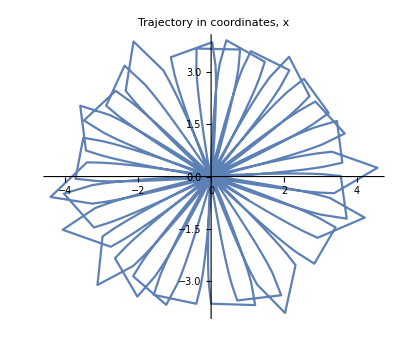

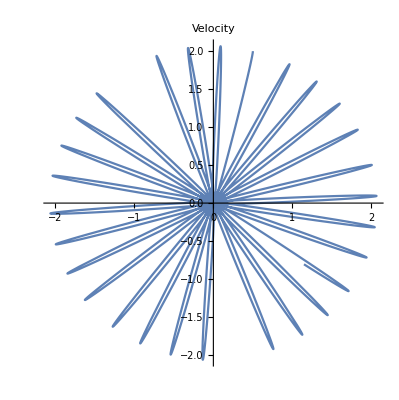

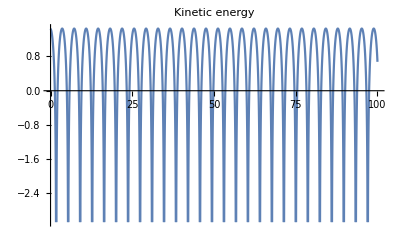

```mathematica
T=100;
sol=NDSolve[{x1'[t]==2v1[t]/(v1[t]^2+v2[t]^2),x2'[t]==2v2[t]/(v1[t]^2+v2[t]^2),v1'[t]==-x1[t],v2'[t]==-x2[t],x1[0]==0.,x2[0]==0.1,v1[0]==0.5,v2[0]==2},{x1,x2,v1,v2},{t,0,T}];
ParametricPlot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,T}, PlotLabel->"Trajectory in coordinates, x"]
ParametricPlot[Evaluate[{v1[t],v2[t]}/.sol],{t,0,T}, PlotLabel->"Velocity"]
Plot[Evaluate[{Log[v1[t]^2+v2[t]^2]}/.sol],{t,0,T}, PlotLabel->"Kinetic energy"]
```

#### 1-d example Roller Coaster / Rough well

Example in Fig. 2 of the paper.

-Graphics-

38.2

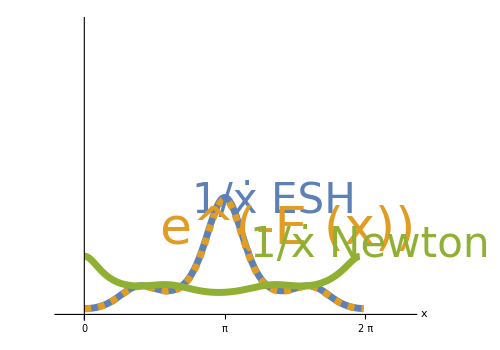

-Graphics-

```mathematica
Clear[g]
img=Rotate[-Graphics-,-0.3];  (*the roller coaster*)
mod[x_]:=2π FractionalPart[x/(2π)];  (*Solution defined on a loop, [0,2π]*)
T=30 π;
En[x_]:=Cos[x] +0.5Cos[3x]; (*A sort of Rough Well based on a Jascha paper*)
g[x_]:=-Sin[x]-3/2Sin[3x];
energyplot=Plot[{En[x]+1.7},{x,-0.1,2π},
AxesOrigin->{0,0}, AxesLabel->{ Style["x",FontSize->42,Opacity[1]],None},
AxesStyle->{Directive[Opacity[0.5],Black],Directive[Opacity[0],Black]},PlotStyle->Thickness[0.01],PlotRange->{{-0.5,2π+1},{0,8}},PlotRangeClipping->False, 
Ticks->{{0,π,2π},None},TicksStyle->FontSize->42,AspectRatio->0.7,ImageSize->500,ImagePadding->All,
Epilog->{Inset[img,{0.18,3.3}], Text[Style["E(x)",FontSize->38,Opacity[1]], {2π+0.6,3.2}]}]
Export["energy_plot.pdf",energyplot];

sol=NDSolve[{x1'[t]==v1[t]/(v1[t]^2),v1'[t]==-g[x1[t]],x1[0]==0,v1[0]==1.},{x1,v1},{t,0,T}];
ham=NDSolve[{x1'[t]==v1[t],v1'[t]==-g[x1[t]],x1[0]==0,v1[0]==1.},{x1,v1},{t,0,T}];

tt=38.2 (*Time for one cycle*)
Plot[Evaluate[{mod[x1[tt t]],v1[tt t]}/.sol],{t,0,1}];
esh=ParametricPlot[
{Evaluate[{mod[x1[t tt]],0.1/x1'[t tt]}/.sol],
Evaluate[{mod[x1[t tt]],0.44Exp[-En[x1[t tt]]]}/.sol],
Evaluate[{mod[x1[t 3.3]],1/x1'[t 3.4]}/.ham]
},
{t,0,1},
AxesOrigin->{0,0}, AxesLabel->{ Style["x",FontSize->42,Opacity[1]],None},AxesStyle->{Directive[Opacity[0.5],Black],Directive[Opacity[0],Black]},PlotStyle->{Thickness[0.01],{CapForm["Butt"],Thickness[0.01],Directive[Dashed]},Thickness[0.01]},PlotRange->{{-0.5,2π+1},{0,5}},PlotRangeClipping->False, AspectRatio->0.7,ImageSize->500,ImagePadding->All,
Ticks->{{0,π,2π},None},TicksStyle->FontSize->42,
Epilog->{Text[Style["1/ẋ ESH",ColorData[97,"ColorList"][[1]], FontSize->42], {π+1.1,1.95}],
Text[Style["e^(-E (x))",ColorData[97,"ColorList"][[2]], FontSize->52], {π+1.4,1.45}],
Text[Style["1/ẋ Newton",ColorData[97,"ColorList"][[3]], FontSize->42], {2π+0.1,1.2}]}]
GraphicsGrid[{{energyplot, esh}},ImageSize->Full]
Export["energy_grid.pdf",%, ImageSize->Full];
```

## 1-d loop animation

1 - d loop animation. E = cos(x).

```mathematica
g[x_]:=-Sin[x];
Clear[esh]
esh=NDSolve[{x1'[t]==v1[t]/(v1[t]^2),v1'[t]==-g[x1[t]],x1[0]==0,v1[0]==0.2},{x1,v1},{t,0, 20 π}];
newton=NDSolve[{x1'[t]==v1[t],v1'[t]==-g[x1[t]],x1[0]==0,v1[0]==0.2},{x1,v1},{t,0,10 π}];
```

4.32475

7.36439

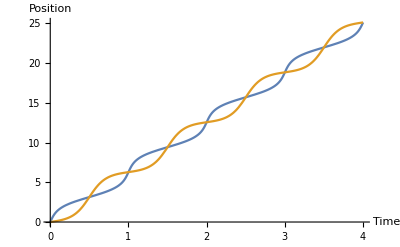

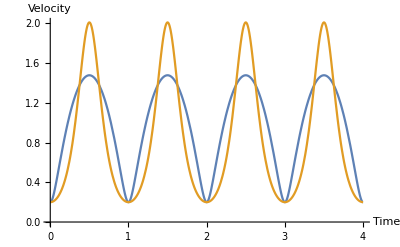

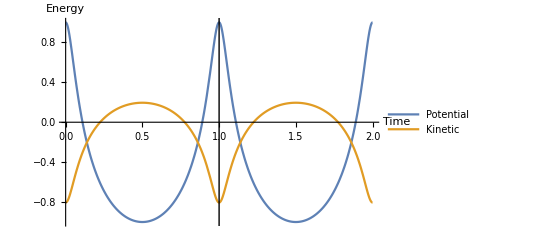

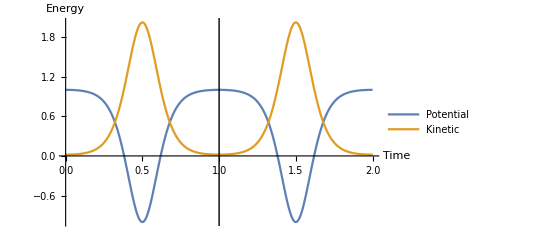

```mathematica
T=Solve[x1[t]==2π/.esh, t][[1,1,2]]
T2=Solve[x1[t]==2π/.newton, t][[1,1,2]]
Plot[{x1[t T]/.esh, x1[t T2]/.newton} ,{t, 0, 4 }, AxesLabel->{"Time","Position"}]
Plot[{v1[t T]/.esh, v1[t T2]/.newton},{t, 0, 4 },AxesLabel->{"Time","Velocity"}]

fs=18;
fs2=14;
e1[tt_]:=Plot[{Cos[x1[t T]]/.esh, 1/2 Log[v1[t T]]/.esh},{t, 0, 2 },AxesLabel->{Style["Time", FontSize->fs],Style["Energy", FontSize->fs]}, PlotLegends->Placed[{Style["Potential",FontSize->fs2], Style["Kinetic",FontSize->fs2]}, {0.75,0.8}],
Epilog->{InfiniteLine[{tt,0},{0,1}]}]
e2[tt_]:=Plot[{Cos[x1[t T2]]/.newton, 1/2 v1[t T2]^2/.newton},{t, 0, 2 },AxesLabel->{Style["Time", FontSize->fs],Style["Energy", FontSize->fs]}, PlotLegends->Placed[{Style["Potential",FontSize->fs2], Style["Kinetic",FontSize->fs2]}, {0.5,0.8}],
Epilog->{InfiniteLine[{tt,0},{0,1}]}]
e1[1]
e2[1]
```

```mathematica
Animate[
GraphicsGrid[
{{Graphics[{Circle[],PointSize[0.05],Point[Evaluate[{Sin[x1[t T]],Cos[x1[t T]]}/.esh]],Text[Style["ESH momentum", FontSize->fs], {0,1.2}]}],
Graphics[{Circle[],PointSize[0.05],Point[Evaluate[{Sin[x1[t T2]],Cos[x1[t T2]]}/.newton]], Text[Style["Newtonian Momentum", FontSize->fs], {0,1.2}]}]},
{e1[t], e2[t]}}, ImageSize->Large],{t,0,2},AnimationRunning->False]
```

```mathematica
gif = Table[
GraphicsGrid[
{{Graphics[{Circle[],PointSize[0.05],Point[Evaluate[{Sin[x1[t T]],Cos[x1[t T]]}/.esh]],Text[Style["ESH momentum", FontSize->fs], {0,1.2}]}],
Graphics[{Circle[],PointSize[0.05],Point[Evaluate[{Sin[x1[t T2]],Cos[x1[t T2]]}/.newton]], Text[Style["Newtonian Momentum", FontSize->fs], {0,1.2}]}]},
{e1[t], e2[t]}}, ImageSize->Large],{t,0,2, 0.01}];
Export["loop.gif", gif]
```

loop.gif